# CS 478

## Scott Leland Crossen

## Nearest Neighbor Project

### Important Note

Please note that the first data set (magic telescope) was too large to be processed in a reasonable amount of time. A reduced set was used to

### Part 1

The code that implements the knn nearest neighbor algorithm is included with the submission of this project. It is written in Scala and follows the functional paradigm. Immutability is observed in all but the underlying learner. Optional distance weighting is included as well.

### Part 2

Note: The magic telescope project is an incredibly large training set with an incredibly large test set. To compensate for the size of this collection, certain modifications were made to the data including selecting a random subset of rows. Under these modifications it is possible that the testing data will produce different accuracy than the model used in comparison.

That said, accuracy showed a maximum around k~14 neighbors. For the most part, normalization did improve accuracy but not by much. Accuracy for normalized k=3 was around .76132. Accuracy for unnormalized data was around .74239.

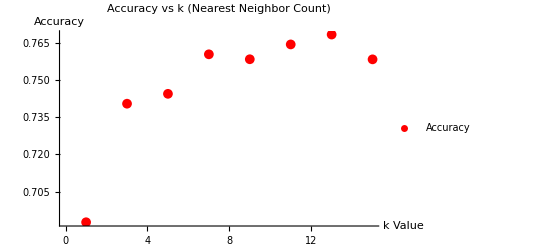

```mathematica
data={0.6926147704590818,0.7405189620758483,0.7445109780439122,0.7604790419161677,0.7584830339321357,0.7644710578842315,0.7684630738522954,0.7584431137724551};
ListPlot[Transpose[{Range[8] 2 -1,data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Accuracy vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}]
```

### Part 3

With odd values of k and distance weighting, the following plot was produced for the mean-squared-error of the housing data. This shows a relative max at around k=7. One interesting behavior of this data is the rather odd discontinuity right before the lowest mean-squared-error is reached. I’m not sure why this is, but perhaps it’s because of the clustered nature of the data with clusters of size 6-7. Another interesting feature of this data is the fact that it appears to asymptote toward a MSE of 6.0. At this point the data is homogenous enough between neighbors.

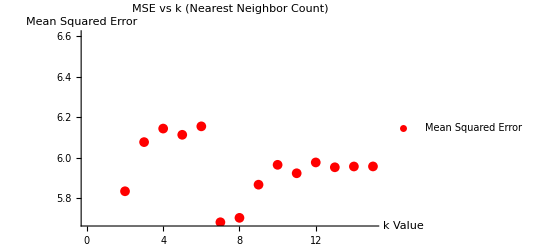

```mathematica
data={7.12995613659747,5.833578514724455,6.076682181577878,6.143658884344705,6.112862636455988,6.1546822028654145,5.680237987398308,5.7020411833058136,5.866070423423278,5.964326635409307,5.922563325333359,5.97614427641325,5.952202094365735,5.9561274606560195,5.95640909319593};
ListPlot[Transpose[{Range[15],data}],AxesLabel->{Style["k Value", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["MSE vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Mean Squared Error"}]
```

### Part 4

The above experiment was repeated for the magic-telescope project. Note again that it was necessary to not use the full dataset based on time considerations. The results indicate the same relative maximum around k=14. The overall accuracy is an increase over the initial tests and goes to show that distance weighting does help in some respect, but not much. The nearest-neighbor optimum did not change

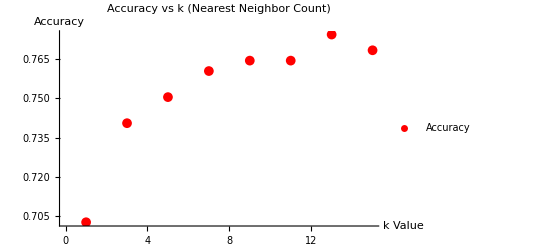

```mathematica
data={0.7026147704590818,0.7405389221556886,0.7505189620758483,0.7604990019960079,0.7644910179640718,0.7644910179640718,0.7744710578842315,0.7684510978043913};
ListPlot[Transpose[{Range[8] 2 -1,data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Accuracy vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}]
```

### Part 5

The below plot shows the accuracy value plotted against k ranged between 1 and 15.

This section required a “categorical” distance metric. To do this, I created a helper function that would take the appropriate columns and compute a quasi-distance double from them. The algorithm is best described below:
1. When comparing two elements of a vector between a training row and a testing row, decompose each vector into elements and call an element-distance metric on them.
2. For quantitative features, use normal distances. For categorical features, compose a list of all other labels that have this same categorical value as the training feature.
3. Do the same with the testing feature
4. For each distinct label possible, count the number of occurrences in each list. Divide number of occurrences by the length of the list.
5. Call the normal distance function between the two resulting values. Sum all possible distances between labels.
6. Return the result.

For this dataset, values of k were iteratively used starting with 1. Eventually (because it was taking a while to compute) I stopped the calculation short of 15 and displayed the results. Seen as only one k-value was requested, this shouldn’t be a problem. A 85/15 split of the data was used between training and testing sets.

As you can see, the desired accuracy of 70-80% was achieved.

As before, it is odd that accuracy decreases as k increases. Perhaps this can be attributed to the fact that the data-set is very singular and doesn’t have many groupings. This fact can be corroborated with the apparent 100% accuracy for a k=1 value. This means that data is obviously duplicated in the data set. Every neighbor that is added then just weakens the hold that the duplicate data has on the testing feature.

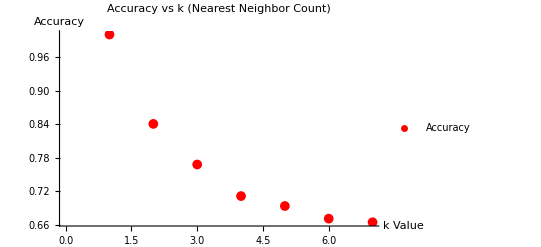

```mathematica
data={1.0,0.8405797101449275,0.7681159420289855,0.711755233494364,0.6940418679549114,0.6714975845410628,0.6650563607085346};
ListPlot[Transpose[{Range[7],data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Accuracy vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}]
```

### Part 6

For this section I wrote a divide-and-conquer pruning algorithm. The algorithm would partition the testing set into n partitions where n is set by the user. Each partition would then be iteratively removed from the data set and (n-1)-fold cross validation would be used on the remaining testing set to judge new accuracy. The partition that received the best accuracy would then recursively call the partitioning function on the best-scored removed-scored subset. The overall subset would be added back to the original set, but each child partition would be iterated over and sequentially removed and the accuracy of the overall test re-gauged recursively. Eventually a base-case would be reached when there was one feature left. The worst-scoring feature would be removed from the testing set if it improved accuracy. This whole process is then repeated until accuracy does not improve.

Below is a plot of accuracy on the housing-price data set. The x-axis represents the divide-and-conquer splitting factor. 2 means the data was split in half at each step, 3 means it was split in thirds, etc. The y axis represents the resulting mean-squared-error of the testing data. Notice that although overall performance is increased when reduction is used but the splitting factor does not matter. The resulting MSE difference appears to just be noise in the data.

For this experiment, k was set at 6 and distance-weighting was used to reduce mean-squared-error.

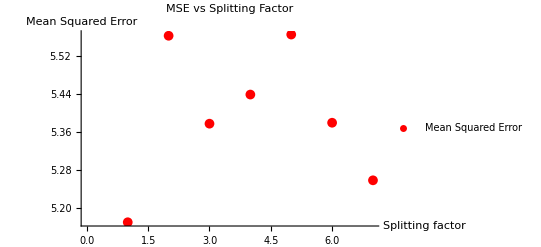

```mathematica
data={5.170726335826066,5.561567758100842,5.377307054302036,5.438346722647866,5.564109839958595,5.379284607312965,5.258637715316816};
ListPlot[Transpose[{Range[7],data}],AxesLabel->{Style["Splitting factor", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["MSE vs Splitting Factor", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Mean Squared Error"}]
```